```mathematica
n
```

```mathematica
(* Note going to work!  Be smarter!!*)
```

```mathematica
(* Change so that we put a while loop around rather than make everything in tables *)
```

```mathematica
mmx=180;
arr=Table[0,{i,1,mmx}];
onecnt=0;
rtsvc={};
rtsint={};
twocnt=0;
rat = 1;
eps = 10^(-8);
k=2;
While[rat≥1/12345 && k <10000,
tb=FindRoot[4^t-2^t-k,{t,Log[5,k]}];
rts=tb[[1,2]];
cds={4^rts,2^rts};
ovls=Select[cds,Abs[#-Round[#]]<eps&];
tp=Abs[rts-Round[rts]];
If[Length[ovls]==2,onecnt++;rtsvc=Append[rtsvc,{rts,k}]];
If[Length[ovls]==2&&tp<eps,twocnt++;rtsint=Append[rtsint,{rts,k}]];
rat=twocnt/onecnt;
If[Mod[k,2 10^5]==0,Print[k," ", rat]];
k++
];
```

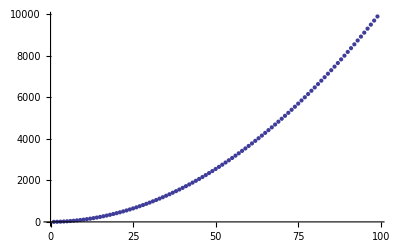

```mathematica
rtsvc;
ListPlot[Transpose[rtsvc][[2]]]
```

```mathematica
Transpose[rtsvc][[2]]
```

{2,6,12,20,30,42,56,72,90,110,132,156,182,210,240,272,306,342,380,420,462,506,552,600,650,702,756,812,870,930,992,1056,1122,1190,1260,1332,1406,1482,1560,1640,1722,1806,1892,1980,2070,2162,2256,2352,2450,2550,2652,2756,2862,2970,3080,3192,3306,3422,3540,3660,3782,3906,4032,4160,4290,4422,4556,4692,4830,4970,5112,5256,5402,5550,5700,5852,6006,6162,6320,6480,6642,6806,6972,7140,7310,7482,7656,7832,8010,8190,8372,8556,8742,8930,9120,9312,9506,9702,9900}

```mathematica
(* We find by experient that the k values which yield roots are given by: *)
kmx = 10^7;
kintmax = 20; (* goes up to 10^(12) *)
ksols=Table[i^2+i,{i,1,kmx}];
kint=Table[4^t-2^t,{t,1,kintmax}];
```

```mathematica
kmaxfil=ksols[[100]]
totmax=209866; (* first value when it is true *)
tot=Take[ksols,{1,totmax}];
int = Select[kint, # ≤Max[tot] &];
{Max[tot],Length[int]/Length[tot],Length[int]/Length[tot]<1/12345}
```

10100

{44043947822,17/209866,True}